Equazione :	y'' - 4 y = 0

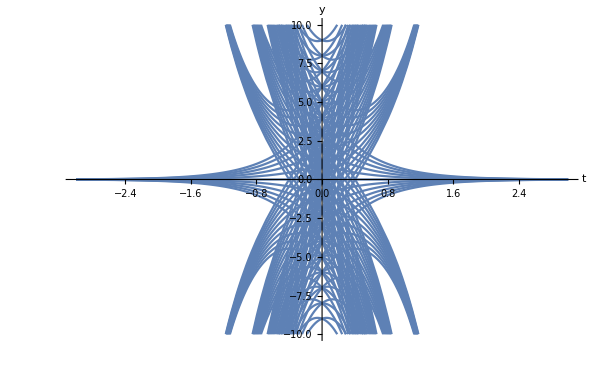
solution = DSolve[y''[t] - 4 y[t] == 0, y[t], t]

{{y[t]→ⅇ^(2 t) C[1]+ⅇ^(-2 t) C[2]}}

f[t_]=y[t]/.solution[[1]]
F[t_]=Table[f[t]/.{C[1]->j,C[2]->r},{j,-5,5},{r,-5,5}]
Plot[F[t],{t,-3,3},AxesLabel->{t,y},PlotRange->{-10,10}]
-Graphics-